```mathematica
fiveNodes = Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];
```

```mathematica
Length[fiveNodes]
```

1024

```mathematica
Table[BaseCoeff[k,"C"],{k,fiveNodes}]//Sort//MatrixRank
```

52

```mathematica
fiveEdges= Select[Keys[allGraphs5],EdgeCount[allGraphs5[#,"graph"]]==5&];
```

```mathematica
Table[
Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],EdgeCount[allGraphs5[#,"graph"]]==count&]}]//Sort//MatrixRank,
{count,10}
]
```

{51,50,51,51,46,46,35,25,10,1}

```mathematica
Table[
Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],EdgeCount[allGraphs6[#,"graph"]]==count&]}]//Sort//MatrixRank,
{count,15}
]
```

{202,201,202,202,202,196,196,196,181,156,155,95,60,15,1}

```mathematica
Table[
Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==count&]}]//Sort//MatrixRank,
{count,6}
]
```

{1,32,122,187,202,203}

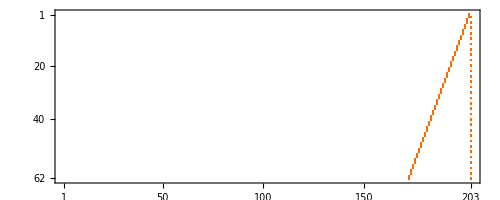

```mathematica
Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==2&]}]//Sort//MatrixPlot
```